```mathematica
city=StringJoin["porto"];
```

## Functions

### EdgeODBetweenessCentrality

```mathematica
EdgeODBetweenessCentrality::usage="EdgeODBetweenessCentrality[OD,G] gives a list of all origini-destination betweenness centralities for the edges in the graph G.";
EdgeODBetweenessCentrality[i_,j_,f_,G_]:=Module[
{b,k,q,P,eid,V,E,numberOfSkippedODPairs,ignoredVolume},
numberOfSkippedODPairs=0;
ignoredVolume=0;
V=VertexList[G];
E=EdgeList[G];
b=Association[Table[PropertyValue[{G,E[[k]]},EdgeLabels]->0,{k,Length[E]}]];
Monitor[
For[k=1,k<=Length[i],k++,
If[And[MemberQ[V,i[[k]]],MemberQ[V,j[[k]]]],
P=FindShortestPath[G,i[[k]],j[[k]]];
For[q=1,q<Length[P],q++,
eid=PropertyValue[{G,P[[q]]->P[[q+1]]},EdgeLabels];
b[eid]+=f[[k]]
],
numberOfSkippedODPairs++;
ignoredVolume+=f[[k]]
];
],
ProgressIndicator[k,{50,Length[i]}]
];
Print["numberOfSkippedODPairs = ",numberOfSkippedODPairs];
Print["ignoredVolume = ",ignoredVolume," (",ignoredVolume/Total[f]," of total volume)"];
Return[b];
];
```

## Graph

### Read edges

#### Read edges data

```mathematica
fid=StringJoin["C:\\Users\\Michael\\Dropbox\\work.network\\code\\matlab\\instances\\mit_data\\instances\\",city,"_edges_algbformat.txt"];
data=Import[fid,"Table","FieldSeparator"->" "];
Take[data,5]//TableForm
```

eid | source | target | dir | capacity | speed_mph | cost_time
20984 | 1 | 7361 | 1 | 950 | 20 | 0.579894
3780 | 1 | 27 | 1 | 950 | 20 | 0.044809
9968 | 2 | 2249 | 1 | 8100 | 40 | 0.439616
7447 | 3 | 9732 | 1 | 5400 | 40 | 0.0824052

#### Unpacking sources, targets and weights of edges

```mathematica
{eid=data[[2;;,1]],source=data[[2;;,2]],target=data[[2;;,3]],weights=data[[2;;,7]]};
```

#### Read node data

```mathematica
fid=StringJoin["C:\\Users\\Michael\\Dropbox\\work.network\\code\\matlab\\instances\\mit_data\\instances\\",city,"_nodes_algbformat.txt"];
data=Import[fid,"Table","FieldSeparator"->" "]; Take[data,5]//TableForm
```

nid | lon | lat
1 | -8.54199 | 41.1299
2 | -8.59126 | 41.1965
3 | -8.62958 | 41.1794
4 | -8.63015 | 41.0924

#### Set nodes

```mathematica
{nid=data[[2;;,1]],lat=data[[2;;,3]],lon=data[[2;;,2]]};
nodes=Table[GeoPosition[{lat[[i]],lon[[i]]}],{i,Length[nid]}];
```

### Graph construction

```mathematica
edges=Table[source[[i]]->target[[i]],{i,Length[eid]}];
labels=Table[edges[[i]]->eid[[i]],{i,Length[eid]}];
coords=Table[{lon[[i]],lat[[i]]},{i,Length[nid]}];
G=Graph[nid,edges,EdgeWeight->weights,EdgeLabels->labels,VertexCoordinates->coords];
EdgesOfG=EdgeList[G];
VertexOfG=VertexList[G];
```

### Plot Graph

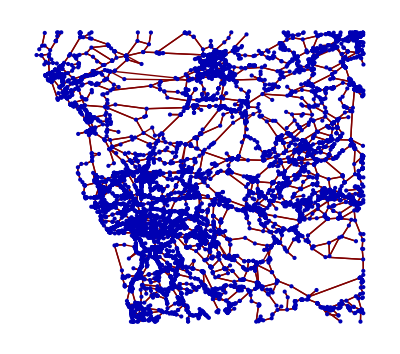

```mathematica
GraphPlot[G,VertexLabeling->False,DirectedEdges->False]
```

## Set Ranks

#### Volume Over Capacity

```mathematica
(*fid=StringJoin["C:\\Users\\Michael\\Dropbox\\work.network\\code\\matlab\\instances\\mit_data\\instances\\",city,"_selfishflows_0_10.txt"];
data=Import[fid,"Table","FieldSeparator"->" "];
Take[data,5]//TableForm*)
```

#### EdgeBetweennessCentrality

```mathematica
Timing[btwc=EdgeBetweennessCentrality[G];]
```

```mathematica
(* export EdgeBetweennessCentrality *)
table=Table[{eid[[i]],EdgesOfG[[i]][[1]],EdgesOfG[[i]][[2]],btwc[[i]]},{i,Length[eid]}];
fid=StringJoin["C:\\Users\\Michael\\gitrepos\\github\\network\\mathematica\\rank_",city,"_edge_betweenness_centrality.csv"];
Export[fid,table,TableHeadings->{"eid","source","target","EdgeBetweennessCentrality"}];
```

#### EdgeODBetweenessCentrality

```mathematica
(* Calculate EdgeODBetweenessCentrality *)
fid=StringJoin["C:\\Users\\Michael\\Dropbox\\work.network\\code\\matlab\\instances\\mit_data\\instances\\",city,"_interod_0_1.txt"];
data=Import[fid,"Table","FieldSeparator"->" "];
Timing[btod=EdgeODBetweenessCentrality[data[[2;;All,1]],data[[2;;All,2]],data[[2;;All,3]],G];]
```

numberOfSkippedODPairs = 54673

$Aborted

```mathematica
(* Export EdgeODBetweennessCentrality *)
table=Table[{eid[[i]],EdgesOfG[[i]][[1]],EdgesOfG[[i]][[2]],btod[[i]]},{i,Length[eid]}];
fid=StringJoin["C:\\Users\\Michael\\Dropbox\\work.network\\code\\matlab\\instances\\mit_data\\figures\\rank_",city,"_edge_od_betweenness_centrality.csv"];
Export[fid,table,TableHeadings->{"eid","source","target","EdgeODBetweennessCentrality"}];
```

## Traffic Assignment

```mathematica
ClearAll[x,c,k,u]
```

```mathematica
Integrate[c*(1+0.15*(u/k)^4),{u,0,x}]
```

c x+(0.03 c x^5)/k^4

```mathematica
Derivative[c*(1+0.15*(u/k)^4),u]
```

Derivative[c (1+(0.15 u^4)/k^4),u]

## BPR

```mathematica
bpr[x]:=c*(1+0.15*(x/k)^4);
```

```mathematica
D[bpr[x],x]
```

(0.6 c x^3)/k^4